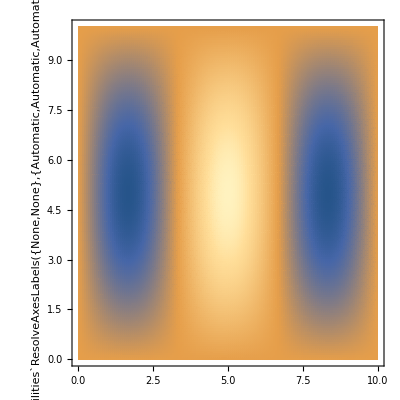
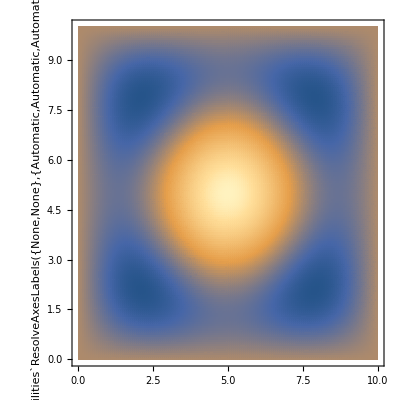
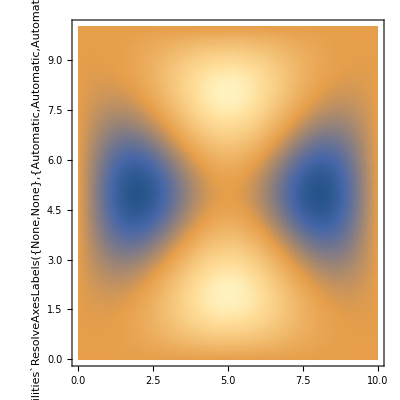

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

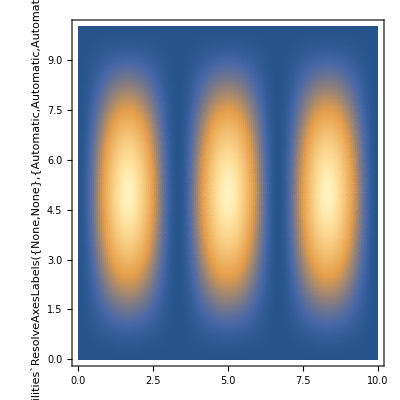
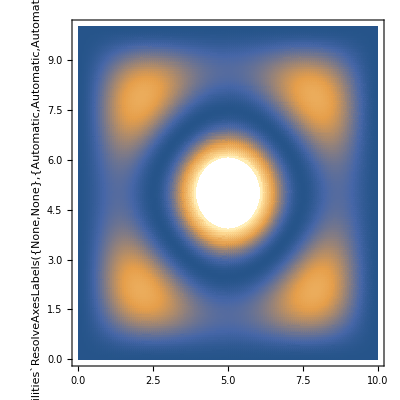
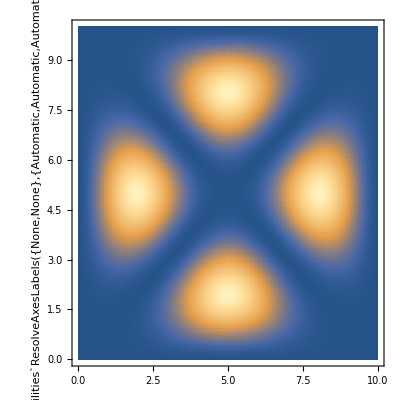

```mathematica
a=10;
n={3,1};
ψ0[x_,i_]:=I Sin[n[[i]]π x/a]Sqrt[2/a]
ψ[x1_,x2_,0]:=ψ0[x1,1]ψ0[x2,2]
ψ[x1_,x2_,1]:=(ψ0[x1,1]ψ0[x2,2]+ψ0[x2,1]ψ0[x1,2])/Sqrt[2]
ψ[x1_,x2_,-1]:=(ψ0[x1,1]ψ0[x2,2]-ψ0[x2,1]ψ0[x1,2])/Sqrt[2]
Table[DensityPlot[ψ[x1,x2,i],{x1,0,a},{x2,0,a},PlotPoints->150],{i,{0,1,-1}}]
Table[Plot3D[ψ[x1,x2,i],{x1,0,a},{x2,0,a},PlotStyle->Directive[White],ExclusionsStyle->{None,Blue},ClippingStyle->None,Mesh->None,Ticks->None,PlotPoints->150],{i,{0,1,-1}}]
Table[DensityPlot[Abs[ψ[x1,x2,i]]^2,{x1,0,a},{x2,0,a},PlotPoints->150],{i,{0,1,-1}}]
```